```mathematica
Needs["Splines`"]
randomizedTube[r1_,r2_,s_,lvls_,d_]:=Module[{ints,bz},
ints = Table[r1+(r2-r1)/lvls*i+{RandomVariate[NormalDistribution[0,d]],RandomVariate[NormalDistribution[0,d]],0},{i,1,lvls-1}];
ints=Join[{r1},ints,{r2}];
bz=BezierCurve[ints];
(*Graphics3D[{Tube[bz,s],Tube[{r1,r2},s]}]*)
Tube[bz,s]
];
```

```mathematica
cm=72/2.54;
(* custom eigensystem *)
Clear[orderedEigensystem]
orderedEigensystem[M_,f_:Re]:=Module[{eigsys, order},
eigsys = Eigensystem[M];
order = Ordering[f[eigsys[[1]]]];
{eigsys[[1,order]],eigsys[[2,order]]ᵀ}
];

(* compute density of states *)
Clear[DOS]
DOS[E_,NE_]:=Module[{min,max,Eints,dos},
{min,max}=MinMax[E];
Eints =min+ Table[(max-min)/NE n,{n,0,NE}];
dos=Table[Length[Nearest[E,e,{Infinity,(max-min)/(2*NE)}]],{e,Eints}];
(*Print[Eints,Length[E]];*)
{Eints,dos/Length[E]}ᵀ
];

(* custom eigensystem *)
Clear[orderedGaugedEigensystem]
orderedGaugedEigensystem[M_,f_:Re]:=Module[{vals,vecs, order,phase,phasemod},
{vals,vecs} = Eigensystem[M];
order = Ordering[f[vals]];
vals=vals[[order]];
vecs=vecs[[order]];
phase = Arg[vecs[[1,1]]];
vecs/=Exp[ⅈ*(phase)];
vecs=vecsᵀ;
{vals,vecs}
];
Clear[regauge]
regauge[v1_,v2_]:=Module[{p1,p1m,p2,p1s,p1f,vf},
p1 = Arg[v1[[1,1]]];
p1m = Mod[p1,2π];
p2 = Arg[v2[[1,1]]];
p1s = Table[p1m+n π,{n,-2,2}];
p1f=Nearest[p1s,Mod[p2,2π]][[1]];
(*Print[StringForm["p_1=`1`, p_2=`2`, p_1/π=`3`, p_(1, f)=`4`",p1, p2,(p1-p2)/π,p1f]];*)
vf =v1* ⅇ^(-ⅈ (p1 - p1f))
];

Clear[Fk,Norb,x,y,Fx,u,ux,Fx, nestedWilsonLoopxky,res,Norb]
nestedWilsonLoopxky[Norb_,res_]:=Module[{Wtilde, W,Wxy,udu,Vxy,Axy,Fxy,phase,prod,ux,u,vals,vecs,vs,Lx,Ly,tr},
{Lx,Ly,tr}=Dimensions[res];
Wtilde={};
W = ConstantArray[0,{Lx,Ly,2,2}];
udu = ConstantArray[0,{Lx,Ly,Norb,tr-Norb}];
Do[
Wxy={};
Vxy={};
Axy={};
Do[
Fxy = IdentityMatrix[Norb];
phase=1;
Do[
u=res[[Mod[x+xp-1,Lx]+1,y,3,2,;;,;;Norb]];
ux=res[[Mod[x+xp,Lx]+1,y,3,2,;;,;;Norb]];
prod = ux†.u;
If[xp==0,udu[[x,y]]=prod];
Fxy=prod.Fxy;
Fxy/=Norm[Fxy]; (* this might stabilize *)
,{x,1,Lx}];
{vals,vecs} = orderedGaugedEigensystem[Fxy,Im];
AppendTo[Wxy,Table[Arg[e]/(2π),{e,vals}]];
AppendTo[Axy,Table[Abs[e],{e,vals}]];
vs=res[[Mod[xp,Lx]+1,y,3,2,;;,;;Norb]].vecs;
If[Vxy≠{}, vs = regauge[vs,Vxy[[-1]]];];
AppendTo[Vxy,vs];
W[[xp+1,y]]=prod;
,{y,1,Ly}];
AppendTo[Wtilde,Eigenvalues[Chop[Product[Vxy[[Mod[n,Length[kys]]+1]]†.Vxy[[n]],{n,Length[kys]}]]]];
,{xp,0,Lx-1}];
{Wxy,Wtilde,Vxy,udu}
]

nestedWilsonLoopykx[Norb_,res_]:=Module[{Wtilde, W,Wxy,udu,Vxy,Axy,Fxy,phase,prod,ux,u,vals,vecs,vs,Lx,Ly,tr},
{Lx,Ly,tr}=Dimensions[res];
Wtilde={};
W = ConstantArray[0,{Lx,Ly,Norb,tr-Norb}];
udu = ConstantArray[0,{Lx,Ly,Norb,tr-Norb}];
Do[
Wxy={};
Vxy={};
Axy={};
Do[
Fxy = IdentityMatrix[Norb];
phase=1;
Do[
u=res[[x,Mod[y+yp-1,Ly]+1,3,2,;;,;;Norb]];
ux=res[[x,Mod[y+yp,Ly]+1,3,2,;;,;;Norb]];
prod = ux†.u;
If[yp==0,udu[[x,y]]=prod];
Fxy=prod.Fxy;
Fxy/=Norm[Fxy]; (* this might stabilize *)
,{y,1,Ly}];
{vals,vecs} = orderedGaugedEigensystem[Fxy,Im];
AppendTo[Wxy,Table[Arg[e]/(2π),{e,vals}]];
AppendTo[Axy,Table[Abs[e],{e,vals}]];
vs=res[[x,Mod[yp,Ly]+1,3,2,;;,;;Norb]].vecs;
If[Vxy≠{}, vs = regauge[vs,Vxy[[-1]]];];
AppendTo[Vxy,vs];
W[[x,yp+1]]=prod;
,{x,1,Lx}];
AppendTo[Wtilde,Eigenvalues[Chop[Product[Vxy[[Mod[n,Length[kys]]+1]]†.Vxy[[n]],{n,Length[kys]}]]]];
,{yp,0,Ly-1}];
{Wxy,Wtilde,Vxy,udu}
]
```

```mathematica
(PauliMatrix[1]+ⅈ PauliMatrix[2])/2
(PauliMatrix[1]-ⅈ PauliMatrix[2])/2
```

```mathematica
Σ[i_,j_]:=KroneckerProduct[PauliMatrix[i],PauliMatrix[j]]
ℍ[kx_,ky_,Σ_]:=(γx+λx Cos[kx])Σ[1,0]-(γy+λy Cos[ky])Σ[2,2]- λx*Cos[kx+ϕx]Σ[2,3]-λy Cos[ky+ϕy]Σ[2,1]
```

```mathematica
Table[DeleteDuplicates[Flatten[ℍ[kx,ky,Σ].Σ[i,j]+Σ[i,j].ℍ[kx,ky,Σ]]]//Length,{i,0,3},{j,0,3}]
ℍ[kx,ky,Σ].Σ[3,0]+Σ[3,0].ℍ[kx,ky,Σ]//DeleteDuplicates
```

```mathematica
Lx=100;Ly=100;
kxs =N[ Table[(2π)/Lx i-π,{i,Lx}]];
kys =N[ Table[(2π)/Ly i-π,{i,Ly}]];
res=Table[{kx,ky,orderedEigensystem[N[ℍ[kx,ky,Σ]]/.{γx->0.,γy->0.2,λx->1,λy->1,ϕx->0π/2,ϕy->0π/2}]},{kx,kxs},{ky,kys}];
spec=Flatten[res,1];
bands=Table[{s[[1]],s[[2]], ev},{s,spec}, {ev,s[[3,1]]}]ᵀ;
```

```mathematica
ListPlot3D[Table[b,{b,bands}],PlotTheme->"Scientific"]
```

```mathematica
Clear[δ,fourierTransform]
δ[x_,y_]=If[x==y,1,0];
delt[t_]:=(δ[Simplify[-I t],0]/.{kx-> 1,ky-> 0}) (δ[Simplify[-I t],0]/.{kx-> 0,ky-> 1});
fourierTransform[ham_,lx_,ly_]:=Module[{Hrs,Hfull},

Hrs[x1_,x2_,y1_,y2_]=(ham*Exp[ⅈ*{kx,ky}.({x1,y1}-{x2,y2})]//TrigToExp//ExpandAll)/.E^sym_-> g[sym]/.{g->delt};
Print[Hrs[x1,x2,y1,y2]];
(* assign local real space Hamiltonian *)
(* now construct the full one *)
Hfull= ConstantArray[0,{lx,ly,4,lx,ly,4}];
Do[
If[x1>0&&x1≤lx&&y2>0&&y2≤ly,
Hfull[[x1,y1,;;,x2,y2,;;]]+=Hrs[x1,x2,y1,y2];
];

,{x1,x2-5,x2+5},{x2,lx},{y1,ly},{y2,y1-5,y1+5}];
ArrayReshape[Hfull,{lx*ly*4,lx*ly*4}]
];
```

```mathematica
ℍrs = fourierTransform[ℍ[kx,ky,Σ]/.{ϕx->π/4,ϕy->π/4},16,8];
```

```mathematica
ListPlot[Table[Eigenvalues[N[ℍrs/.{γx->g, γy->g,λx->1, λy->1}]]//Sort,{g,-1,1,0.2}]ᵀ,PlotTheme->"Scientific",Joined->True]
```

```mathematica
L=9
lx=L;ly=L;
ℍos= ConstantArray[0,{lx,ly,4,lx,ly,4}];
Do[
ℍos[[x,y,2,x,y,1]]+=γx1;
ℍos[[x,y,4,x,y,3]]+=γx2;
ℍos[[x,y,3,x,y,2]]+=γy1;
ℍos[[x,y,1,x,y,4]]+=γy2;
,{x,lx},{y,ly}];
ℍnn= ConstantArray[0,{lx,ly,4,lx,ly,4}];
Do[
ℍnn[[x+1,y,4,x,y,3]]+=λx1;
ℍnn[[x,y,2,x+1,y,1]]+=λx2;
,{x,lx-1},{y,ly}];
Do[
ℍnn[[x,y+1,1,x,y,4]]+=λy1;
ℍnn[[x,y,3,x,y+1,2]]+=λy2;
,{x,lx},{y,ly-1}];
Hrs=ArrayReshape[ℍos+ℍnn,{lx*ly*4,lx*ly*4}];
Hrs=Hrs+Hrs†;
gs=Table[g,{g,-2,2,0.025}];
red=RGBColor[152/255,30/255,20/255];
```

9

```mathematica
<<MaTeX`
Monitor[
spec1=Table[Sort[Eigenvalues[Hrs/.{γx1->g ⅇ^(ⅈ π/2),γx2->g,γy1->g,γy2->g,λx1->1,λx2->1,λy1->ⅇ^(ⅈ π/2),λy2->1}]],{g,gs}];,g]
```

```mathematica
tns=Thickness[0.005];Clear[tickFunc]
tickFunc=Charting`ScaledTicks[{Identity,Identity},TicksLength->{.05,.025}][##]&;
```

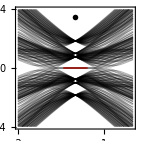

```mathematica
sl=60;
inset1=ListPlot[spec1ᵀ[[2 L^2-1;;2 L^2+2,sl;;-sl]],DataRange->{gs[[sl]],gs[[-sl]]},PlotStyle->Directive[red,tns],Joined->True];
p1= Show[ListPlot[spec1ᵀ,Joined->True,GridLines->None,PlotTheme->"Scientific",PlotRange->{-4,4},PlotRangePadding->0,DataRange->{-2,2},AspectRatio->1,ImageSize->5cm,FrameLabel->MaTeX[{"g","\\varepsilon"}],FrameStyle->Directive[Thin,Black],PlotStyle->Directive[tns,Black, Opacity[0.3]],FrameTicks->{{tickFunc,None},{tickFunc,None}}],inset1,Epilog->Inset[MaTeX["(a)"],{0,3.5},{Center,Center}]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["BBH.jpg",p1,ImageResolution->600]
```

/Users/andreas.haller/mathematica_files

BBH.jpg

```mathematica
<<MaTeX`
Monitor[
spec2=Table[Sort[Eigenvalues[Hrs/.{γx1->g ⅇ^(ⅈ π/2),γx2->g,γy1->g,γy2->g,λx1->1,λx2->1.5,λy1->1.5 ⅇ^(ⅈ π/2),λy2->1}]],{g,gs}];,g]
```

$Aborted

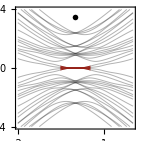

```mathematica
sl=60;tns=Thickness[0.005];
inset2=ListPlot[spec2ᵀ[[2 L^2-1;;2 L^2+2,sl;;-sl]],DataRange->{gs[[sl]],gs[[-sl]]},PlotStyle->Directive[red,tns],Joined->True];
p2= Show[ListPlot[spec2ᵀ,Joined->True,GridLines->None,PlotTheme->"Scientific",PlotRange->{-4,4},PlotRangePadding->0,DataRange->{-2,2},AspectRatio->1,ImageSize->5cm,FrameLabel->MaTeX[{"g","\\varepsilon"}],FrameStyle->Directive[Thin,Black],PlotStyle->Directive[tns,Black, Opacity[0.3]],FrameTicks->{{tickFunc,None},{tickFunc,None}}],inset2,Epilog->Inset[MaTeX["(b)"],{0,3.5},{Center,Center}]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["BBH_broken_mirrors.jpg",p2,ImageResolution->600]
```

/Users/andreas.haller/mathematica_files

BBH_broken_mirrors.jpg

```mathematica
L=3
lx=L;ly=L;
ℍos= ConstantArray[0,{lx,ly,4,lx,ly,4}];
Do[
ℍos[[x,y,2,x,y,1]]+=γx1;
ℍos[[x,y,4,x,y,3]]+=γx2;
ℍos[[x,y,3,x,y,2]]+=γy2;
ℍos[[x,y,1,x,y,4]]+=γy1;
,{x,lx},{y,ly}];
ℍnn= ConstantArray[0,{lx,ly,4,lx,ly,4}];
Do[
ℍnn[[x+1,y,4,x,y,3]]+=λx1;
ℍnn[[x,y,2,x+1,y,1]]+=λx2;
,{x,lx-1},{y,ly}];
Do[
ℍnn[[x,y+1,1,x,y,4]]+=λy1;
ℍnn[[x,y,3,x,y+1,2]]+=λy2;
,{x,lx},{y,ly-1}];
Hrs=ArrayReshape[ℍos+ℍnn,{lx*ly*4,lx*ly*4}];
Hrs=Hrs+Hrs†;
gs=Table[g,{g,-2,2,0.025}];
red=RGBColor[152/255,30/255,20/255];
```

3

```mathematica
gsel = 0.4;fs=28;
Hlatt=ArrayReshape[Hrs/.{γx1->gsel ⅇ^(ⅈ π/2),γx2->gsel,γy1->gsel,γy2->gsel,λx1->1,λx2->1.5,λy1->1.5 ⅇ^(ⅈ π/2),λy2->1},{lx,ly,4,lx,ly,4}];
cfun=ColorData["Pastel"]
dcs=DeleteDuplicates[Abs[Arg[Hlatt//Flatten]]]
ncols=Length[dcs];
cols = Table[cfun[i/ncols],{i,ncols}]
ucd=.2;
sublatt=ucd*{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}};
latt = Flatten[Table[{x,y,0}+b,{x,lx},{y,ly},{b,sublatt}],2];
conn = Flatten[Table[{{x1,y1,0}+sublatt[[b1]],{x2,y2,0}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
lbl1={Text[MaTeX[StringForm["\\gamma_{`1`}",#[[2]]],FontSize->fs],#[[1]]]&/@{{{2,2.35,0},"x,1"},{{2,1.95,0},"x,2"},{{1.6,1.0,0},"y,1"},{{2.0,1.0,0},"y,2"}}};
lbl2={Text[MaTeX[StringForm["\\lambda_{`1`}",#[[2]]],FontSize->fs],#[[1]]]&/@{{{2.5,2.35,0},"x,1"},{{2.5,1.95,0},"x,2"},{{1.6,1.5,0},"y,1"},{{2.0,1.5,0},"y,2"}}};
sps =Table[{n,0.1},{n,latt}];
p3=Graphics3D[Join[lbl1,lbl2,{Black,Sphere[#,0.1]}&/@latt,{{cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],Tube[{#[[1]],#[[2]]},#[[3,1]]*0.03]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic"]
```

ColorDataFunction[…]

{0,1.5708}

{RGBColor[0.9584254999999999, 0.877884, 0.5906629999999999],RGBColor[0.431296, 0.709773, 0.927077]}

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["BBH_symm_broken.jpg",p3,ImageResolution->600]
```

/Users/andreas.haller/mathematica_files

BBH_symm_broken.jpg

```mathematica
gsel = 0.4
Hlatt=ArrayReshape[Hrs/.{γx1->gsel ⅇ^(ⅈ π/4),γx2->gsel ⅇ^(ⅈ π/4),γy1->gsel,γy2->gsel,λx1->1.0,λx2->1.0,λy1->1. ⅇ^(ⅈ π/4),λy2->1.0 ⅇ^(ⅈ π/4)},{lx,ly,4,lx,ly,4}];
cfun=ColorData["Pastel"]
dcs=DeleteDuplicates[Abs[Arg[Hlatt//Flatten]]]
ncols=Length[dcs];
cols = Table[cfun[i/ncols],{i,ncols}]
ucd=.2;
sublatt=ucd*{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}};
latt = Flatten[Table[{x,y,0}+b,{x,lx},{y,ly},{b,sublatt}],2];
conn = Flatten[Table[{{x1,y1,0}+sublatt[[b1]],{x2,y2,0}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
sps =Table[{n,0.1},{n,latt}];
p4=Graphics3D[Join[lbl1,lbl2,{Black,Sphere[#,0.1]}&/@latt,{{cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],Tube[{#[[1]],#[[2]]},#[[3,1]]*0.03]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic"]
```

0.4

ColorDataFunction[…]

{0,0.785398}

{RGBColor[0.9584254999999999, 0.877884, 0.5906629999999999],RGBColor[0.431296, 0.709773, 0.927077]}

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]]
Export["BBH_symm.jpg",p4,ImageResolution->600]
```

/Users/andreas.haller/mathematica_files

BBH_symm.jpg

```mathematica
gsel = 0.
Hlatt=ArrayReshape[Hrs/.{γx1->gsel,γx2->gsel,γy1->gsel,γy2->gsel,λx1->1.0,λx2->1.0,λy1->1.,λy2->1.0},{lx,ly,4,lx,ly,4}];
cfun=ColorData["Pastel"]
dcs=DeleteDuplicates[Abs[Arg[Hlatt//Flatten]]]
ncols=Length[dcs];
cols = Table[cfun[i/ncols],{i,ncols}];
cols={cfun[0.5]};
ucd=.2;
sublatt=ucd*{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}};
latt = Flatten[Table[{x,y,0}+b,{x,lx},{y,ly},{b,sublatt}],2];
latt1=latt;
conn = Flatten[Table[{{x1,y1,0}+sublatt[[b1]],{x2,y2,0}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
lbl1={Text[MaTeX[StringForm["\\gamma_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2,2.3,0},"x,1"},{{2,1.9,0},"x,2"},{{1.65,2.05,0},"y,1"},{{2.05,2.05,0},"y,2"}}};
lbl2={Text[MaTeX[StringForm["\\lambda_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2.5,2.3,0},"x,1"},{{2.5,1.9,0},"x,2"},{{1.65,2.5,0},"y,1"},{{2.05,2.5,0},"y,2"}}};
sps =Table[{n,0.1},{n,latt}];

bl1=Graphics3D[Join[{Black,Sphere[#,0.1]}&/@latt,{{cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],Tube[{#[[1]],#[[2]]},#[[3,1]]*0.03]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic"];

latt = Flatten[Table[{x,y,1}+b,{x,lx},{y,ly},{b,sublatt}],2];
latt2=latt;
conn = Flatten[Table[{{x1,y1,1}+sublatt[[b1]],{x2,y2,1}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
lbl1={Text[MaTeX[StringForm["\\gamma_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2,2.3,0},"x,1"},{{2,1.9,0},"x,2"},{{1.65,2.05,0},"y,1"},{{2.05,2.05,0},"y,2"}}};
lbl2={Text[MaTeX[StringForm["\\lambda_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2.5,2.3,0},"x,1"},{{2.5,1.9,0},"x,2"},{{1.65,2.5,0},"y,1"},{{2.05,2.5,0},"y,2"}}};
sps =Table[{n,0.1},{n,latt}];
bl2=Graphics3D[Join[{Black,Sphere[#,0.1]}&/@latt,{{cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],Tube[{#[[1]],#[[2]]},#[[3,1]]*0.03]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic"];
```

0.

ColorDataFunction[…]

{0}

```mathematica
inodes=Table[{2,2,0}+b,{b,sublatt}]
int=Graphics3D[{cfun[0],Opacity[0.3],EdgeForm[None],Tube[{#,#+{0,0,1}},.07]}&/@latt]
```

{{1.8,1.8,0.},{2.2,1.8,0.},{2.2,2.2,0.},{1.8,2.2,0.}}

-Graphics3D-

```mathematica
p=Show[bl1,bl2,Graphics3D[{Text[MaTeX["s=\\uparrow"],{2.75,0,1}],Text[MaTeX["s=\\downarrow"],{2.75,0,0}]}],int,ViewPoint->{π/4,π/2,π/7},Boxed->False]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["H1.jpg",p,ImageResolution->600]
```

H1.jpg

```mathematica
gsel = 0.
Hlatt=ArrayReshape[Hrs/.{γx1->gsel,γx2->gsel,γy1->gsel,γy2->gsel,λx1->1.0,λx2->1.0,λy1->1.,λy2->1.0},{lx,ly,4,lx,ly,4}];
cfun=ColorData["Pastel"]
dcs=DeleteDuplicates[Abs[Arg[Hlatt//Flatten]]]
ncols=Length[dcs];
cols = Table[cfun[i/ncols],{i,ncols}];
cols={Gray};
ucd=.2;
sublatt=ucd*{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}};
latt = Flatten[Table[{x,y,0}+b,{x,lx},{y,ly},{b,sublatt}],2];
latt1=latt;
conn = Flatten[Table[{{x1,y1,0}+sublatt[[b1]],{x2,y2,0}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
lbl1={Text[MaTeX[StringForm["\\gamma_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2,2.3,0},"x,1"},{{2,1.9,0},"x,2"},{{1.65,2.05,0},"y,1"},{{2.05,2.05,0},"y,2"}}};
lbl2={Text[MaTeX[StringForm["\\lambda_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2.5,2.3,0},"x,1"},{{2.5,1.9,0},"x,2"},{{1.65,2.5,0},"y,1"},{{2.05,2.5,0},"y,2"}}};
sps =Table[{n,0.1},{n,latt}];

latt=Graphics3D[Join[{Black,Sphere[#,0.1]}&/@latt,{{cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],Tube[{#[[1]],#[[2]]},#[[3,1]]*0.03]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic"]
```

0.

ColorDataFunction[…]

{0}

-Graphics3D-

```mathematica
gsel=1;lsel=0;
Hlatt=ArrayReshape[Hrs/.{γx1->gsel,γx2->gsel,γy1->gsel,γy2->gsel,λx1->lsel,λx2->lsel,λy1->lsel,λy2->lsel},{lx,ly,4,lx,ly,4}];
cfun=ColorData["Pastel"]
dcs=DeleteDuplicates[Abs[Arg[Hlatt//Flatten]]]
ncols=Length[dcs];
cols = Table[cfun[i/ncols],{i,ncols}];
cols={cfun[1]};
ucd=.2;
sublatt=ucd*{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}};
latt = Flatten[Table[{x,y,0}+b,{x,lx},{y,ly},{b,sublatt}],2];
latt1=latt;
conn = Flatten[Table[{{x1,y1,0}+sublatt[[b1]],{x2,y2,0}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
lbl1={Text[MaTeX[StringForm["\\gamma_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2,2.3,0},"x,1"},{{2,1.9,0},"x,2"},{{1.65,2.05,0},"y,1"},{{2.05,2.05,0},"y,2"}}};
lbl2={Text[MaTeX[StringForm["\\lambda_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2.5,2.3,0},"x,1"},{{2.5,1.9,0},"x,2"},{{1.65,2.5,0},"y,1"},{{2.05,2.5,0},"y,2"}}};
sps =Table[{n,0.1},{n,latt}];

latt1=Graphics3D[Join[{Black,Sphere[#,0.1]}&/@latt,{{Opacity[0.15],cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],randomizedTube[#[[1]],#[[2]],#[[3,1]]*0.03,1,0.1]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic"]
```

ColorDataFunction[…]

{0}

-Graphics3D-

```mathematica
gsel=0;lsel=1;
Hlatt=ArrayReshape[Hrs/.{γx1->gsel,γx2->gsel,γy1->gsel,γy2->gsel,λx1->lsel,λx2->lsel,λy1->lsel,λy2->lsel},{lx,ly,4,lx,ly,4}];
cfun=ColorData["Pastel"]
dcs=DeleteDuplicates[Abs[Arg[Hlatt//Flatten]]]
ncols=Length[dcs];
cols = Table[cfun[i/ncols],{i,ncols}];
cols={cfun[0.5]};
ucd=.2;
sublatt=ucd*{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}};
latt = Flatten[Table[{x,y,0}+b,{x,lx},{y,ly},{b,sublatt}],2];
latt1=latt;
conn = Flatten[Table[{{x1,y1,0}+sublatt[[b1]],{x2,y2,0}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
lbl1={Text[MaTeX[StringForm["\\gamma_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2,2.3,0},"x,1"},{{2,1.9,0},"x,2"},{{1.65,2.05,0},"y,1"},{{2.05,2.05,0},"y,2"}}};
lbl2={Text[MaTeX[StringForm["\\lambda_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2.5,2.3,0},"x,1"},{{2.5,1.9,0},"x,2"},{{1.65,2.5,0},"y,1"},{{2.05,2.5,0},"y,2"}}};
sps =Table[{n,0.1},{n,latt}];

nnc=Graphics3D[Join[{Black,Sphere[#,0.1]}&/@latt,{{cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],Tube[{#[[1]],#[[2]]},#[[3,1]]*0.03]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic"]
```

ColorDataFunction[…]

{0}

-Graphics3D-

```mathematica
gsel=1;lsel=0;
Hlatt=ArrayReshape[Hrs/.{γx1->gsel,γx2->gsel,γy1->gsel,γy2->gsel,λx1->lsel,λx2->lsel,λy1->lsel,λy2->lsel},{lx,ly,4,lx,ly,4}];
cfun=ColorData["Pastel"]
dcs=DeleteDuplicates[Abs[Arg[Hlatt//Flatten]]]
ncols=Length[dcs];
cols = Table[cfun[i/ncols],{i,ncols}];
cols={cfun[0.]};
ucd=.2;
sublatt=ucd*{{-1,-1,0},{1,-1,0},{1,1,0},{-1,1,0}};
latt = Flatten[Table[{x,y,0}+b,{x,lx},{y,ly},{b,sublatt}],2];
latt1=latt;
conn = Flatten[Table[{{x1,y1,0}+sublatt[[b1]],{x2,y2,0}+sublatt[[b2]],AbsArg[Hlatt[[x1,y1,b1,x2,y2,b2]]]},{x1,lx},{y1,ly},{x2,lx},{y2,ly},{b1,Length[sublatt]},{b2,Length[sublatt]}],5];
lbl1={Text[MaTeX[StringForm["\\gamma_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2,2.3,0},"x,1"},{{2,1.9,0},"x,2"},{{1.65,2.05,0},"y,1"},{{2.05,2.05,0},"y,2"}}};
lbl2={Text[MaTeX[StringForm["\\lambda_{`1`}",#[[2]]],FontSize->18],#[[1]]]&/@{{{2.5,2.3,0},"x,1"},{{2.5,1.9,0},"x,2"},{{1.65,2.5,0},"y,1"},{{2.05,2.5,0},"y,2"}}};
sps =Table[{n,0.1},{n,latt}];

int=Graphics3D[Join[{Black,Sphere[#,0.1]}&/@latt,{{Opacity[0.2],cols[[Position[dcs,Abs[#[[3,2]]]][[1,1]]]],Tube[{#[[1]],#[[2]]},#[[3,1]]*0.07]}&/@conn}],ViewPoint->Top,ViewProjection->"Orthographic"]
```

ColorDataFunction[…]

{0}

-Graphics3D-

```mathematica
p=Show[nnc,int];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["H2.jpg",p,ImageResolution->600]
```

H2.jpg